```mathematica
a=1
k=1
V=100
Z[Te_,N1_,En_]:= k*Te*Log[(V/(√(a/Te)))^N1 / N1!]*Exp[-En/Te]
```

1

1

100

```mathematica
D[Z[Te,N1,0],Te]
```

N1/2+Log[(100^N1 (1/Te)^(-N1/2))/(N1!)]

```mathematica
Simplify[%]
```

N1/2+Log[(100^N1 (1/Te)^(-N1/2))/(N1!)]

```mathematica
Z1[Te_,N1_,ene_]:= k*Te*Log[(V/(1))^N1 / N1!]*Exp[-ene/Te]
```

```mathematica
D[Z1[Te,N1,0],Te]
```

Log[100^N1/(N1!)]

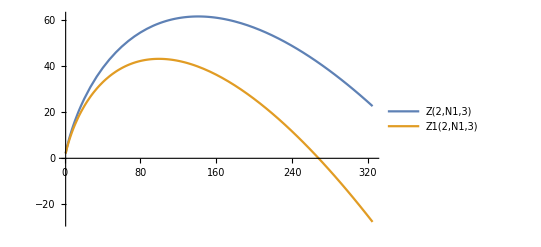

```mathematica
Plot[{Z[2,N1,3],Z1[2,N1,3]},{N1,1,325}, PlotLegends->"Expressions"]
```

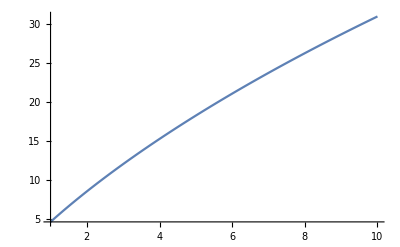

```mathematica
Plot[Z1[1,N1,0],{N1,1,10}]
```

```mathematica
Z1  [1,3,0]
```

Log[500000/3]

```mathematica
Z[1,3,0]
```

Log[500000/3]

```mathematica
Entro[N3_]:= N3*(Log[1000/N3]+3/2)
```

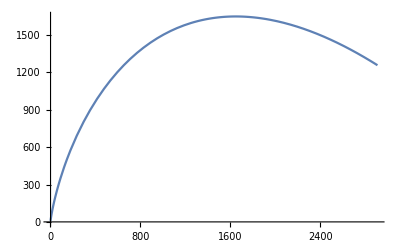

```mathematica
Plot[Entro[N3], {N3,1,2909}]
```

```mathematica
D[Entro[N3],N3]
```

1/2+Log[1000/N3]

```mathematica
Log[0.5]
```

-0.693147

```mathematica
N[Log[10]]
```

```mathematica
2.302585092994046
G1[N4_]:=2^N4/N4!
```

2.30259

```mathematica
FAV[N5_]:=D[G1[N5],N5]
```

```mathematica
Plot[FAV [N4],{N4,0,5}]
```

General::ivar: 0.000102143 is not a valid variable.

General::ivar: 0.102143 is not a valid variable.

General::ivar: 0.204184 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

```mathematica
FAV[3]
```

General::ivar: 3 is not a valid variable.

∂_3 4/3

```mathematica
fun[z_]:=z*Log[100/z]
```

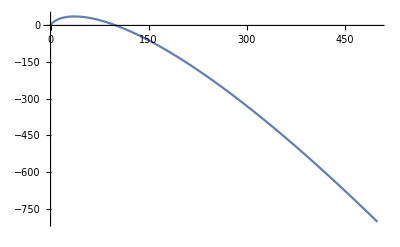

```mathematica
Plot[fun [N4],{N4,0,500}]
```

```mathematica
Bolt[Nt_,k_]:= Binomial[k+Nt-1,k]
```

```mathematica
Bolt[6,9]
```

2002

```mathematica
Bolt[7,3]
```

84